```mathematica
$Assumptions=A∈Integers&&A>2&&a∈Reals&&a>0&&Λ∈Reals&&Λ>0&&R∈Reals&&r∈Reals;
```

### LECs definition

```mathematica
hbarc=197.3161329;
mN=938.91852/hbarc;
λ={0.05,0.1,0.16,0.2,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.9,0.95,1,1.05,1.1,1.2,1.5,2,3,4,6,10};
CC={-1.552,-2.242,-3.440,-4.040,-6.397,-7.808,-9.310,-10.976,-12.782,-14.726,-16.809,-19.032,-21.394,-23.894,-26.536,-32.234,-35.291,-38.489,-41.824,-45.299,-52.666,-78.111,-131.646,-280.457,-484.921,-1060.797,-2880.387};
LeCdat=ReadList["LeC_fit.dat",{Number,Number}];
DD={-0.324,-0.246,0.019,0.223,1.207,1.981,2.828,3.913,5.209,6.718,8.468,10.463,12.734,15.276,18.137,24.813,28.664,32.911,37.527,42.570,53.971,100.476,232.413,854.107,2495.364,16915.630,756723.220};
```

InterpolatingFunction::dmval: Input value {0.00286} lies outside the range of data in the interpolating function. Extrapolation will be used.

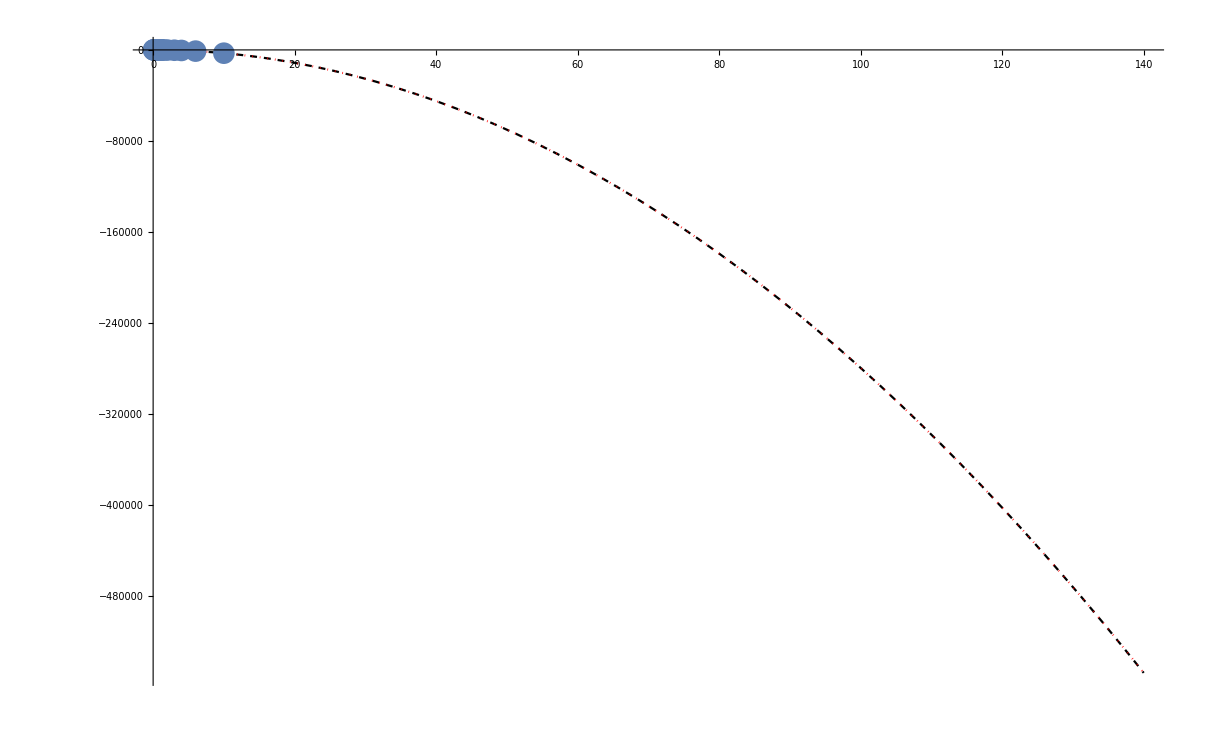

```mathematica
CL=Interpolation[Transpose[{λ,CC}]];
CL2=Interpolation[LeCdat];
Plot[{CL[x],CL2[x]},{x,0,140},PlotStyle->{{Black,Dashed},{Red,Dotted}}];
Show[%,ListPlot[Transpose[{λ,CC}]]]
```

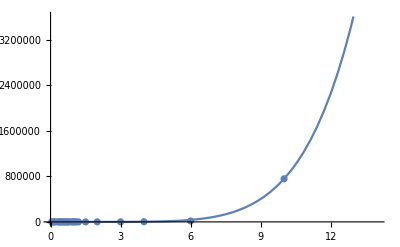

```mathematica
model=c+a x+b x^2+d x^3+e x^4+f x^5+g x^6;
fit=FindFit[Transpose[{λ,DD}],{model,c>0,a>0,b>0,d>0,e>0,f>0,g>0},{a,b,c,d,e,f,g},x];
DL=Function[{x},Evaluate[model/.fit]];
Plot[DL[x],{x,0,14}];
Show[%,ListPlot[Transpose[{λ,DD}]]]
```

## |A| - |1|

### V̂=𝟙 (norm & exchange kernel)

```mathematica
ϵr2[A_?NumberQ]:=(3- A^-1);
ϵrr[A_?NumberQ]:=2 (1-A^-1);

MnoIntDi[nbr_?NumberQ]:=4 a IdentityMatrix[nbr-1]+(ConstantArray[2 a,{nbr-1,nbr-1}]-2 a IdentityMatrix[nbr-1]); 

MnoIntEx[nbr_?NumberQ]:=a ϵr2[nbr] IdentityMatrix[nbr-1]+(ConstantArray[a/2 ϵrr[nbr],{nbr-1,nbr-1}]-a/2 ϵrr[nbr] IdentityMatrix[nbr-1]); 
NnoIntEx[nbr_?NumberQ]:=ConstantArray[a nbr^-1 R+I s (1+nbr^-1),(nbr-1)];

dbg=2;testA=15;
For[nbr1=2,nbr1<4,nbr1++,{

Mex=MnoIntEx[nbr1]; 
Nex=NnoIntEx[nbr1];

Mdi=MnoIntDi[nbr1];

Kα=Simplify[CoefficientList[Simplify[ 1/2 Nex.Inverse[Mex].Nex],s]];

MexS=-2 Kα[[3]];
NexS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2;

If[dbg==2,Print["A = ",nbr1,"   ",Grid[Mex//MatrixForm,Nex//MatrixForm]],Sinn=1];
If[dbg==2,Print["A = ",nbr1,"   Kα = ",Kα],Sinn=1];
If[dbg==2,Print["A = ",nbr1,"   ",MexS,"   ",NexS],Sinn=1];

FakDi=Det[Mdi];
FakEx=Simplify[Det[Mex] MexS];
ExpEx=Simplify[MonomialList[(1/2 NexS^2/MexS+expR2),R]];

Print["A = ",nbr1,"   ;   |M_norm| =  ",Expand[Simplify[FakDi]],"\n            |M_exch| =  ",Expand[Simplify[FakEx]],"  ;  α_𝟙 =  ",ExpEx[[1]],"  ;  β_𝟙 =   ",ExpEx[[2]],";  γ_𝟙 =   ",ExpEx[[3]],"\n"];

}]
```

A = 2   Grid[((5 a)/2),((a R)/2+(3 ⅈ s)/2)]

A = 2   Kα = {(a R^2)/20,(3 ⅈ R)/10,-9/(20 a)}

A = 2   9/(10 a)   ⅈ (r+R/2)+(3 ⅈ R)/10

A = 2   ;   |M_norm| =  4 a
            |M_exch| =  9/4  ;  α_𝟙 =  -(5 a R^2)/9  ;  β_𝟙 =   -8/9 a r R;  γ_𝟙 =   -(5 a r^2)/9

A = 3   Grid[((8 a)/3 | (2 a)/3
(2 a)/3 | (8 a)/3),((a R)/3+(4 ⅈ s)/3
(a R)/3+(4 ⅈ s)/3)]

A = 3   Kα = {(a R^2)/30,(4 ⅈ R)/15,-8/(15 a)}

A = 3   16/(15 a)   ⅈ (r+R/3)+(4 ⅈ R)/15

A = 3   ;   |M_norm| =  12 a^2
            |M_exch| =  (64 a)/9  ;  α_𝟙 =  -(15 a R^2)/32  ;  β_𝟙 =   -9/16 a r R;  γ_𝟙 =   -(15 a r^2)/32

#### Recurrence relations for norm and Exchange Kernels

```mathematica
Clear[A,Λ,a,nbr1,R,r];

normfac[A_]:=FindSequenceFunction[{4,12,32,80,192,448,1024,2304,5120},A-1];

fz[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 8^2,102400,69696 4},A-1];
fn[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

az[A_]:=FindSequenceFunction[{5,15,34,65,111,175,260,369},A-1];
abcn[A_]:=FindSequenceFunction[{9,32,75,144,245,384,567,800},A-1];
bz[A_]:=FindSequenceFunction[{8,18,32,50,72,98,128,162},A-1];

alphaNormEx[A_,a_]:=Simplify[a az[A]/abcn[A]];
betaNormEx[A_,a_]:=Simplify[a bz[A]/abcn[A]];
gammaNormEx[A_,a_]:=Simplify[a gz[A]/abcn[A]];
gz=az; (* hermiticity contraint *)

ExpoNormEx[A_,a_,R_,r_]:=Exp[-R^2 alphaNormEx[A,a]-betaNormEx[A,a] r R-gammaNormEx[A,a] r^2];

PreFacNormDiNenner[A_,a_]:=normfac[A] a^(A-1);
PreFacNormDi[A_,a_]:= (Sqrt[(2 Pi)^(A-1)/PreFacNormDiNenner[A,a]])^(3);

Print["\nNorm: ∫d^3UnderBar[r̄]_(1 ..  A - 1)^2e^(-2 a ∑(SuperscriptBox[r, 2] + rr)) = ",PreFacNormDi[A,a]]

PreFacNormExNenner[A_,a_]:=((fz[A]/fn[A]) a^(A-2));
PreFacNormEx[A_,a_]:=Simplify[((Sqrt[(2 Pi)^(A-1)/PreFacNormExNenner[A,a]])^(3)) PreFacNormDi[A,a]^(-1)];

Print[Row[{"ζ_1 =  ",PreFacNormEx[A,a],"  ;  α_1 =  ",
Simplify[alphaNormEx[A,a]],"   ;  β_1 =  ",Simplify[betaNormEx[A,a]],"    ;  γ_1 =  ",Simplify[gammaNormEx[A,a]]
}]]

Clear[A,a,R,r];

Print["\nExKernel: Det(M_exch) e^(-SubscriptBox[α, 𝟙 - Ex] R^2 - SubscriptBox[β, 𝟙 - Ex] r^2 - SubscriptBox[γ, 𝟙 - Ex] Rr) =  (",PreFacNormEx[A,a],")·",ExpoNormEx[A,a,R,r]]
```

Norm: ∫d^3UnderBar[r̄]_(1 ..  A - 1)^2e^(-2 a ∑(SuperscriptBox[r, 2] + rr)) = ((a^(1-A) π^(-1+A))/A)^(3/2)

ζ_1 =  (2 √2)/((((-1+A) (1+A)^2)/(a A^3))^(3/2))  ;  α_1 =  (a (A+A^3))/(2 (-1+A) (1+A)^2)   ;  β_1 =  (2 a A^2)/((-1+A) (1+A)^2)    ;  γ_1 =  (a (A+A^3))/(2 (-1+A) (1+A)^2)

ExKernel: Det(M_exch) e^(-SubscriptBox[α, 𝟙 - Ex] R^2 - SubscriptBox[β, 𝟙 - Ex] r^2 - SubscriptBox[γ, 𝟙 - Ex] Rr) =  ((2 √2)/((((-1+A) (1+A)^2)/(a A^3))^(3/2)))·ⅇ^(-(a (A+A^3) r^2)/(2 (-1+A) (1+A)^2)-(2 a A^2 r R)/((-1+A) (1+A)^2)-(a (A+A^3) R^2)/(2 (-1+A) (1+A)^2))

#### performance version

```mathematica
PreFacNormDi[A,a]//InputForm
```

((a^(1 - A)*Pi^(-1 + A))/A)^(3/2)

```mathematica
iPreFacNormDi[A_,a_]:=((a^(1-A)*Pi^(-1+A))/A)^(3/2);
```

```mathematica
PreFacNormEx[A,a]//InputForm
```

(2*Sqrt[2])/(((-1 + A)*(1 + A)^2)/(a*A^3))^(3/2)

```mathematica
zeta1[A_,a_]:=(2*Sqrt[2])/(((-1+A)*(1+A)^2)/(a*A^3))^(3/2);
```

```mathematica
alphaNormEx[A,a]//InputForm
```

(a*(A + A^3))/(2*(-1 + A)*(1 + A)^2)

```mathematica
ialfNormEx[A_,a_]:=(a*(A+A^3))/(2*(-1+A)*(1+A)^2);
```

```mathematica
betaNormEx[A,a]//InputForm
```

(2*a*A^2)/((-1 + A)*(1 + A)^2)

```mathematica
ibetNormEx[A_,a_]:=(2*a*A^2)/((-1+A)*(1+A)^2);
```

```mathematica
gammaNormEx[A,a]//InputForm
```

(a*(A + A^3))/(2*(-1 + A)*(1 + A)^2)

```mathematica
igamNormEx[A_,a_]:=(a*(A+A^3))/(2*(-1+A)*(1+A)^2);
```

```mathematica
Animate[
Plot[{ialfNormEx[AA,aa],ibetNormEx[AA,aa],igamNormEx[AA,aa]
},{AA,2,8},PlotLegends->{α,β,γ},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"A/a"}],
{aa,1.,5},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

### V̂=C_2· ∑_(i<A)δ_Λ((r̄)_i+R) (2NI direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=0;testA=3;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{

M2Di=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N2Di=Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M2Di;
inhom=N2Di;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/4 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M| =  ",Expand[Simplify[PreFak]],"    ;  α =   ",Simplify[Expo[[1]]]];

}]
```

A = 3      ;    |M| =  12 a^2+2 a Λ^2    ;  α =   -(3 a R^2 Λ^2)/(2 (6 a+Λ^2))

A = 4      ;    |M| =  32 a^3+6 a^2 Λ^2    ;  α =   -(4 a R^2 Λ^2)/(16 a+3 Λ^2)

A = 5      ;    |M| =  80 a^4+16 a^3 Λ^2    ;  α =   -(5 a R^2 Λ^2)/(4 (5 a+Λ^2))

A = 6      ;    |M| =  192 a^5+40 a^4 Λ^2    ;  α =   -(6 a R^2 Λ^2)/(24 a+5 Λ^2)

A = 7      ;    |M| =  448 a^6+96 a^5 Λ^2    ;  α =   -(7 a R^2 Λ^2)/(28 a+6 Λ^2)

A = 8      ;    |M| =  1024 a^7+224 a^6 Λ^2    ;  α =   -(8 a R^2 Λ^2)/(32 a+7 Λ^2)

A = 9      ;    |M| =  2304 a^8+512 a^7 Λ^2    ;  α =   -(9 a R^2 Λ^2)/(36 a+8 Λ^2)

A = 10      ;    |M| =  5120 a^9+1152 a^8 Λ^2    ;  α =   -(10 a R^2 Λ^2)/(40 a+9 Λ^2)

A = 11      ;    |M| =  11264 a^10+2560 a^9 Λ^2    ;  α =   -(11 a R^2 Λ^2)/(44 a+10 Λ^2)

A = 12      ;    |M| =  24576 a^11+5632 a^10 Λ^2    ;  α =   -(12 a R^2 Λ^2)/(48 a+11 Λ^2)

#### Recurrence relations 2NI Direct

```mathematica
Clear[A,Λ,a,R,x];
sa[A_]:=FindSequenceFunction[{4,12,32,80,192,448},A-1];
saΛ[A_]:=FindSequenceFunction[{1/2,2,6,16,40,96},A-1];
sexpn1[A_]:=FindSequenceFunction[{8,12,16,20,24,28},A-1];
alpha2NIDi[A_,a_,Λ_]:=Simplify[A Λ^2/(sexpn1[A]+(A-1) Λ^2/a)];

PreFac2NIDiNenner[A_,a_,Λ_]:=sa[A] a^(A-1)+saΛ[A] a^(A-2) Λ^2;
PreFac2NIDi[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-1)/PreFac2NIDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];
Expo2NIDi[A_,a_,Λ_,R_]:=Exp[-alpha2NIDi[A,a,Λ] R^2];

Which[
dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac2NIDiNenner[testA,a,Λ],"  ;  α =  ",
alpha2NIDi[testA,a,Λ]
}]],
dbg==0,
Print[Row[{"η_1 = C_0· ",Simplify[(A-1) PreFac2NIDi[A,a,Λ]],"  ;  κ_1 =  ",
Simplify[alpha2NIDi[A,a,Λ]]
}]],
dbg==-1,
Print[Row[{"η_1 = C_0· ",TeXForm[Simplify[(A-1) PreFac2NIDi[A,a,Λ]]],"  ;  κ_1 =  ",
TeXForm[Simplify[alpha2NIDi[A,a,Λ]]]
}]]
];

Clear[A,a,Λ,R,x];
If[dbg==1,
Print["\n2NI Direct:          Det(M) e^(-α R^2) =  (",PreFac2NIDiNenner[testA,a,Λ],")·",Expo2NIDi[testA,a,Λ,R]]
];
```

η_1 = C_0· (8 (-1+A))/((4+((-1+A) Λ^2)/(a A))^(3/2))  ;  κ_1 =  (a A Λ^2)/(4 a A+(-1+A) Λ^2)

```mathematica
Series[Simplify[(A-1) PreFac2NIDi[A,a,Λ]],{Λ,0,4}]
```

(-1+A)-(3 (-1+A)^2 Λ^2)/(8 (a A))+(15 (-1+A)^3 Λ^4)/(128 a^2 A^2)+O[Λ]^5

#### performance version

```mathematica
PreFac2NIDi[A,a,Λ]//InputForm
```

8/(4 + ((-1 + A)*Λ^2)/(a*A))^(3/2)

```mathematica
eta2NIDi[A_,a_,Λ_]:=8/(4+((-1+A)*Λ^2)/(a*A))^(3/2);
```

```mathematica
Simplify[alpha2NIDi[A,a,Λ]]//InputForm
```

(a*A*Λ^2)/(4*a*A + (-1 + A)*Λ^2)

```mathematica
kappa2NIDi[A_,a_,Λ_]:=(a*A*Λ^2)/(4*a*A+(-1+A)*Λ^2);
```

```mathematica
(PreFac2NIDi[A,a,Λ] Expo2NIDi[A,a,Λ,R])//InputForm
```

8/(E^((a*A*R^2*Λ^2)/(4*a*A + (-1 + A)*Λ^2))*(4 + ((-1 + A)*Λ^2)/(a*A))^(3/2))

```mathematica
i2NIDi[A_,a_,Λ_,R_]:=8/(E^((a*A*R^2*Λ^2)/(4*a*A+(-1+A)*Λ^2))*(4+((-1+A)*Λ^2)/(a*A))^(3/2));
```

```mathematica
AA=4;
Animate[
Plot[{kappa2NIDi[AA,aa,LL]
},{LL,0.4,4},PlotLegends->{κ},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"Λ"}],
{aa,0.2,3,Appearance->"Labeled"},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (ARM) direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=0;testA=3;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,7],nbr1++,{

M3armDi=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[(i==1&&j==2)||(i==2&&j==1),-Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armDi=Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armDi;
inhom=N3armDi;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/4 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M_𝟙| =  ",Expand[Simplify[PreFak]],"    ;  α_𝟙 =   ",Simplify[Expo[[1]]]];

}]
```

A = 3      ;    |M_𝟙| =  12 a^2+8 a Λ^2+Λ^4/4    ;  α_𝟙 =   -(6 a R^2 Λ^2 (2 a+Λ^2))/(48 a^2+32 a Λ^2+Λ^4)

A = 4      ;    |M_𝟙| =  32 a^3+22 a^2 Λ^2+a Λ^4    ;  α_𝟙 =   -(4 a R^2 Λ^2 (2 a+Λ^2))/(32 a^2+22 a Λ^2+Λ^4)

A = 5      ;    |M_𝟙| =  80 a^4+56 a^3 Λ^2+3 a^2 Λ^4    ;  α_𝟙 =   -(10 a R^2 Λ^2 (2 a+Λ^2))/(80 a^2+56 a Λ^2+3 Λ^4)

A = 6      ;    |M_𝟙| =  192 a^5+136 a^4 Λ^2+8 a^3 Λ^4    ;  α_𝟙 =   -(3 a R^2 Λ^2 (2 a+Λ^2))/(24 a^2+17 a Λ^2+Λ^4)

#### Recurrence relations 3NI ARM Direct

```mathematica
Clear[A];
dbg=0;
c3armdief1[A_]:=FindSequenceFunction[{12,32,80,192,448,1024,2304},A-2];
c3armdief2[A_]:=FindSequenceFunction[{8,22,56,136,320,736,1664},A-2];
c3armdief3[A_]:=FindSequenceFunction[{1/4,1,3,8,20,48,112,256},A-2];

c3armdiexpz1[A_]:=FindSequenceFunction[{12,16,20,24,28,32,36},A-2];
c3armdiexpz2[A_]:=FindSequenceFunction[{6,8,10,12},A-2];

c3armdiexpn1[A_]:=FindSequenceFunction[{48,64,80,96,112,128},A-2];
c3armdiexpn2[A_]:=FindSequenceFunction[{32,44,56,68,80,92,104},A-2];
c3armdiexpn3[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7,8},A-2];

alpha3NIarmDi[A_,a_,Λ_]:=Simplify[Λ^2 (c3armdiexpz1[A] a^2+c3armdiexpz2[A] a Λ^2)/(c3armdiexpn1[A] a^2+c3armdiexpn2[A] a Λ^2+c3armdiexpn3[A] Λ^4)];
PreFac3NIarmDiNenner[A_,a_,Λ_]:=Simplify[c3armdief1[A] a^(A-1)+c3armdief2[A] a^(A-2) Λ^2+c3armdief3[A] a^(A-3) Λ^4];
PreFac3NIarmDi[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-1)/PreFac3NIarmDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];
Expo3NIarmDi[A_,a_,Λ_,R_]:=Exp[- alpha3NIarmDi[A,a,Λ] R^2];

Which[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac3NIarmDiNenner[testA,a,Λ],"  ;  α =  ",
alpha3NIarmDi[testA,a,Λ]
}]],
dbg==0,
Print[Row[{"η_2 = SubscriptBox[D, 1]/2· ",Simplify[(A-1) (A-2) PreFac3NIarmDi[A,a,Λ]],"   ;   κ_2 =  ",
Simplify[alpha3NIarmDi[A,a,Λ]]
}]],
dbg==-1,
Print[Row[{"η_2 = SubscriptBox[D, 1]/2· ",TeXForm[Simplify[(A-1) (A-2) PreFac3NIarmDi[A,a,Λ]]],TeXForm["\nκ_2 =  "],TeXForm[
Simplify[alpha3NIarmDi[A,a,Λ]]]
}]]
];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-ARM Direct:            Det(M) e^(-α R^2) =    (",PreFac3NIarmDiNenner[testA,a,Λ],")·",Expo3NIarmDi[testA,a,Λ,R]]
];
```

η_2 = SubscriptBox[D, 1]/2· 64 a^3 (-2+A) (-1+A) (A/(16 a^2 A+4 a (-1+3 A) Λ^2+(-2+A) Λ^4))^(3/2)   ;   κ_2 =  (2 a A Λ^2 (2 a+Λ^2))/(16 a^2 A+4 a (-1+3 A) Λ^2+(-2+A) Λ^4)

```mathematica
Series[Simplify[(A-1) (A-2) PreFac3NIarmDi[A,a,Λ]],{Λ,0,4}]
```

(-2+A) (-1+A)+(3 (1-3 A) (-2+A) (-1+A) Λ^2)/(8 a A)+(3 (-2+A) (-1+A) (5-22 A+41 A^2) Λ^4)/(128 a^2 A^2)+O[Λ]^5

#### performance version

```mathematica
PreFac3NIarmDi[A,a,Λ]//InputForm
```

64*a^3*(A/(16*a^2*A + 4*a*(-1 + 3*A)*Λ^2 + (-2 + A)*Λ^4))^(3/2)

```mathematica
eta3NIarmDi[A_,a_,Λ_]:=64*a^3*(A/(16*a^2*A+4*a*(-1+3*A)*Λ^2+(-2+A)*Λ^4))^(3/2);
```

```mathematica
Simplify[alpha3NIarmDi[A,a,Λ]]//InputForm
```

(2*a*A*Λ^2*(2*a + Λ^2))/(16*a^2*A + 4*a*(-1 + 3*A)*Λ^2 + (-2 + A)*Λ^4)

```mathematica
kappa3NIarmDi[A_,a_,Λ_]:=(2*a*A*Λ^2*(2*a+Λ^2))/(16*a^2*A+4*a*(-1+3*A)*Λ^2+(-2+A)*Λ^4);
```

```mathematica
(PreFac3NIarmDi[A,a,Λ] Expo3NIarmDi[A,a,Λ,R])//InputForm
```

(64*a^3*(A/(16*a^2*A + 4*a*(-1 + 3*A)*Λ^2 + (-2 + A)*Λ^4))^(3/2))/
 E^((2*a*A*R^2*Λ^2*(2*a + Λ^2))/(16*a^2*A + 4*a*(-1 + 3*A)*Λ^2 + (-2 + A)*Λ^4))

```mathematica
i3NIarmDi[A_,a_,Λ_,R_]:=(64*a^3*(A/(16*a^2*A+4*a*(-1+3*A)*Λ^2+(-2+A)*Λ^4))^(3/2))/E^((2*a*A*R^2*Λ^2*(2*a+Λ^2))/(16*a^2*A+4*a*(-1+3*A)*Λ^2+(-2+A)*Λ^4));
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i+R)δ_Λ((r̄)_j+R)] (3NI (STAR) direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=0;testA=9;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{

M3starDi=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3starDi=Table[If[i==1||i==2,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3starDi;
inhom=N3starDi;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/2 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M| =  ",Expand[Simplify[PreFak]],"    ;  α =   ",Simplify[Expo[[1]]]];

}]
```

A = 3      ;    |M| =  12 a^2+4 a Λ^2+Λ^4/4    ;  α =   -(6 a R^2 Λ^2)/(12 a+Λ^2)

A = 4      ;    |M| =  32 a^3+12 a^2 Λ^2+a Λ^4    ;  α =   -(4 a R^2 Λ^2)/(8 a+Λ^2)

A = 5      ;    |M| =  80 a^4+32 a^3 Λ^2+3 a^2 Λ^4    ;  α =   -(10 a R^2 Λ^2)/(20 a+3 Λ^2)

A = 6      ;    |M| =  192 a^5+80 a^4 Λ^2+8 a^3 Λ^4    ;  α =   -(3 a R^2 Λ^2)/(6 a+Λ^2)

A = 7      ;    |M| =  448 a^6+192 a^5 Λ^2+20 a^4 Λ^4    ;  α =   -(14 a R^2 Λ^2)/(28 a+5 Λ^2)

A = 8      ;    |M| =  1024 a^7+448 a^6 Λ^2+48 a^5 Λ^4    ;  α =   -(8 a R^2 Λ^2)/(16 a+3 Λ^2)

A = 9      ;    |M| =  2304 a^8+1024 a^7 Λ^2+112 a^6 Λ^4    ;  α =   -(18 a R^2 Λ^2)/(36 a+7 Λ^2)

A = 10      ;    |M| =  5120 a^9+2304 a^8 Λ^2+256 a^7 Λ^4    ;  α =   -(5 a R^2 Λ^2)/(2 (5 a+Λ^2))

A = 11      ;    |M| =  11264 a^10+5120 a^9 Λ^2+576 a^8 Λ^4    ;  α =   -(22 a R^2 Λ^2)/(44 a+9 Λ^2)

A = 12      ;    |M| =  24576 a^11+11264 a^10 Λ^2+1280 a^9 Λ^4    ;  α =   -(12 a R^2 Λ^2)/(24 a+5 Λ^2)

#### Recurrence relations 3NI STAR Direct

```mathematica
Clear[A];
sl0s[A_]:=FindSequenceFunction[{4,12,32,80,192,448},A-1];
sl2s[A_]:=FindSequenceFunction[{4,12,32,80,192,448,1024},A-2];
sl4s[A_]:=FindSequenceFunction[{1/4,1,3,8,20,48,112,256},A-2];

sexpz1s[A_]:=FindSequenceFunction[{6,8,10,12,14,16,18},A-2];
sexpn0s[A_]:=FindSequenceFunction[{12,16,20,24,28,32,36,40},A-2];
sexpn2s[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7,8},A-2];

alpha3NIstarDi[A_,a_,Λ_]:=Simplify[a Λ^2 sexpz1s[A]/(sexpn0s[A] a+sexpn2s[A] Λ^2)];
PreFac3NIstarDiNenner[A_,a_,Λ_]:=Simplify[sl0s[A] a^(A-1)+sl2s[A] a^(A-2) Λ^2+sl4s[A] a^(A-3) Λ^4];
PreFac3NIstarDi[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-1)/PreFac3NIstarDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];
Expo3NIstarDi[A_,a_,Λ_,R_]:=Exp[-alpha3NIstarDi[A,a,Λ] R^2];

Which[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac3NIstarDiNenner[testA,a,Λ],"  ;  α =  ",
alpha3NIstarDi[testA,a,Λ]
}]],dbg==0,
Print[Row[{"η_3 = SubscriptBox[D, 1]/2· ",Simplify[(A-1) (A-2) PreFac3NIstarDi[A,a,Λ]],"  ;  κ_3 =  ",
alpha3NIstarDi[A,a,Λ]
}]],dbg==-1,
Print[Row[{"η_3 = SubscriptBox[D, 1]/2· ",TeXForm[Simplify[(A-1) (A-2) PreFac3NIstarDi[A,a,Λ]]],"\nκ_3 =  ",
TeXForm[alpha3NIstarDi[A,a,Λ]]
}]]
];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-STAR Direct:         Det(M) e^(-α R^2) =  (",PreFac3NIstarDiNenner[testA,a,Λ],")·",Expo3NIstarDi[testA,a,Λ,R]]
];
```

η_3 = SubscriptBox[D, 1]/2· (64 (-2+A) (-1+A))/((((4 a+Λ^2) (4 a A+(-2+A) Λ^2))/(a^2 A))^(3/2))  ;  κ_3 =  (2 a A Λ^2)/(4 a A+(-2+A) Λ^2)

```mathematica
Series[Simplify[(A-1) (A-2) PreFac3NIstarDi[A,a,Λ]],{Λ,0,4}]
```

(-2+A) (-1+A)-(3 ((-2+A) (-1+A)^2) Λ^2)/(4 (a A))+(3 (-2+A) (-1+A) (5-8 A+4 A^2) Λ^4)/(32 a^2 A^2)+O[Λ]^5

performance version

```mathematica
PreFac3NIstarDi[A,a,Λ]//InputForm
```

64/(((4*a + Λ^2)*(4*a*A + (-2 + A)*Λ^2))/(a^2*A))^(3/2)

```mathematica
eta3NIstarDi[A_,a_,Λ_]:=64/(((4*a+Λ^2)*(4*a*A+(-2+A)*Λ^2))/(a^2*A))^(3/2);
```

```mathematica
Simplify[alpha3NIstarDi[A,a,Λ]]//InputForm
```

(2*a*A*Λ^2)/(4*a*A + (-2 + A)*Λ^2)

```mathematica
kappa3NIstarDi[A_,a_,Λ_]:=(2*a*A*Λ^2)/(4*a*A+(-2+A)*Λ^2);
```

```mathematica
(PreFac3NIstarDi[A, a, Λ] Expo3NIstarDi[A, a, Λ, R]) // InputForm
```

64/(E^((2*a*A*R^2*Λ^2)/(4*a*A + (-2 + A)*Λ^2))*(((4*a + Λ^2)*(4*a*A + (-2 + A)*Λ^2))/(a^2*A))^(3/2))

```mathematica
i3NIstarDi[A_,a_,Λ_,R_]:=64/(E^((2*a*A*R^2*Λ^2)/(4*a*A+(-2+A)*Λ^2))*(((4*a+Λ^2)*(4*a*A+(-2+A)*Λ^2))/(a^2*A))^(3/2));
```

```mathematica
AA=4;
Animate[
Plot[{kappa3NIarmDi[AA,aa,LL],kappa3NIstarDi[AA,aa,LL]
},{LL,0.4,4},PlotLegends->{Subscript[κ, 2],Subscript[κ, 3]},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"Λ"}],
{aa,0.2,3,Appearance->"Labeled"},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

#### Plot direct interaction kernels

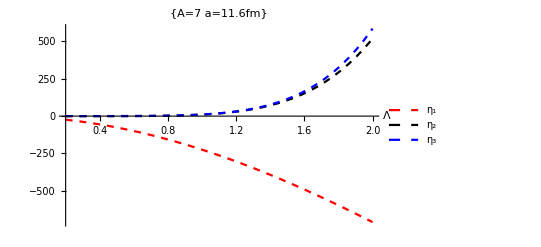

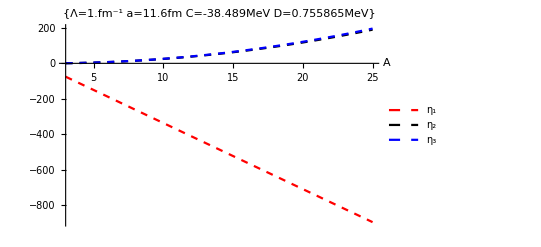

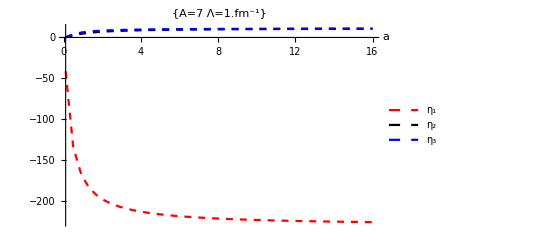

```mathematica
AA=7;
aa=11.6;
LA=1.0;
Plot[
{CL[LL] (AA-1) PreFac2NIDi[AA,aa,LL],
0.5 DL[LL] (AA-1) (AA-2) PreFac3NIarmDi[AA,aa,LL],0.5 DL[LL] (AA-1) (AA-2) PreFac3NIstarDi[AA,aa,LL]},{LL,0.2,2},PlotPoints->40,MaxRecursion->0,PlotLegends->{"η_1","η_2","η_3"},PlotStyle->{{Red,Dashed},{Black,Dashed},{Blue,Dashed}},AxesLabel->{"Λ"},PlotLabel->{"A="<>ToString[AA]<>"  a="<>ToString[aa]<>"fm"}]
Plot[
{CL[LA] (Aa-1) PreFac2NIDi[Aa,aa,LA],
0.5 DL[LA] (Aa-1) (Aa-2) PreFac3NIarmDi[Aa,aa,LA],0.5 DL[LA] (Aa-1) (Aa-2) PreFac3NIstarDi[Aa,aa,LA]},{Aa,3,25},PlotPoints->40,MaxRecursion->0,PlotLegends->{"η_1","η_2","η_3"},PlotStyle->{{Red,Dashed},{Black,Dashed},{Blue,Dashed}},AxesLabel->{"A"},PlotLabel->{"Λ="<>ToString[LA]<>"fm^-1   a="<>ToString[aa]<>"fm   C="<>ToString[CL[LA]]<>"MeV     D="<>ToString[DL[LA]]<>"MeV"}]
Plot[
{CL[LA] (AA-1) PreFac2NIDi[AA,aa,LA],
0.5 DL[LA] (AA-1) (AA-2) PreFac3NIarmDi[AA,aa,LA],0.5 DL[LA] (AA-1) (AA-2) PreFac3NIstarDi[AA,aa,LA]},{aa,0.1,16.0},PlotPoints->40,MaxRecursion->0,PlotLegends->{"η_1","η_2","η_3"},PlotStyle->{{Red,Dashed},{Black,Dashed},{Blue,Dashed}},AxesLabel->{"a"},PlotLabel->{"A="<>ToString[AA]<>"  Λ="<>ToString[LA]<>"fm^-1"}]
```

```mathematica
Clear[A,a,Λ,R];
AA1=24;aa1=6;Lam1=4;
AA2=24;aa2=6;Lam2=4;
Rmax=2;
myStyle4=Grid[{{Style["A_1 = "<>ToString[AA1]<>"   a_1 = "<>ToString[aa1]<>" fm^-2"<>"   Λ_1 = "<>ToString[Lam1]<>" fm^-1     (V̂)_(2  NI)+(V̂)_(3  NI)",Black]},{Style["A_2 = "<>ToString[AA2]<>"   a_2 = "<>ToString[aa2]<>" fm^-2"<>"   Λ_2 = "<>ToString[Lam2]<>" fm^-1     (V̂)_(2  NI)",Blue]}}];
Animate[
Plot[{
(AA1/(AA1+1)) (0.5 DL[Lam1] (AA1-1) (AA1-2) (i3NIarmDi[AA1,aa1,Lam1,r]+i3NIstarDi[AA1,aa1,Lam1,r])+
CL[Lam1] (AA1-1) i2NIDi[AA1,aa1,Lam1,r]),(AA1/(AA1+1)) (0.5 DL[Lam2] (AA2-1) (AA2-2) (i3NIarmDi[AA2,aa2,Lam2,r]+i3NIstarDi[AA2,aa2,Lam2,r])+CL[Lam2] (AA2-1) i2NIDi[AA2,aa2,Lam2,r])
},{r,0,Rmax},PlotPoints->40,MaxRecursion->0,PlotLegends->{},PlotLabel->myStyle4,PlotStyle->{{Black,Dashed},{Blue,Dashed}},AxesLabel->{"R"}],
{Lam1,0.05,12},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

### V̂=C_2· ∑_(i<A)δ_Λ((r̄)_i+R) (2NI EX interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=0;testA=9;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{

M2Ex=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N2Ex=NnoIntEx[nbr1]+Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M2Ex;
inhom=N2Ex;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/4 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
}]
```

A = 3   ;  |M_EX| =  (64 a)/9+(8 Λ^2)/9  ;  α_EX =  -(3 a R^2 (5 a+4 Λ^2))/(4 (8 a+Λ^2))   ;  β_EX =  -(9 a r R (2 a+Λ^2))/(4 (8 a+Λ^2))    ;  γ_EX =  -(3 a r^2 (5 a+Λ^2))/(4 (8 a+Λ^2))

A = 4   ;  |M_EX| =  (75 a^2)/4+(25 a Λ^2)/8  ;  α_EX =  -(2 a R^2 (34 a+27 Λ^2))/(25 (6 a+Λ^2))   ;  β_EX =  -(32 a r R (2 a+Λ^2))/(25 (6 a+Λ^2))    ;  γ_EX =  -(2 a r^2 (34 a+7 Λ^2))/(25 (6 a+Λ^2))

A = 5   ;  |M_EX| =  (1152 a^3)/25+(216 a^2 Λ^2)/25  ;  α_EX =  -(5 a R^2 (52 a+41 Λ^2))/(36 (16 a+3 Λ^2))   ;  β_EX =  -(25 a r R (2 a+Λ^2))/(9 (16 a+3 Λ^2))    ;  γ_EX =  -(5 a r^2 (52 a+11 Λ^2))/(36 (16 a+3 Λ^2))

A = 6   ;  |M_EX| =  (980 a^4)/9+(196 a^3 Λ^2)/9  ;  α_EX =  -(3 a R^2 (37 a+29 Λ^2))/(49 (5 a+Λ^2))   ;  β_EX =  -(36 a r R (2 a+Λ^2))/(49 (5 a+Λ^2))    ;  γ_EX =  -(3 a r^2 (37 a+8 Λ^2))/(49 (5 a+Λ^2))

A = 7   ;  |M_EX| =  (12288 a^5)/49+(2560 a^4 Λ^2)/49  ;  α_EX =  -(7 a R^2 (50 a+39 Λ^2))/(32 (24 a+5 Λ^2))   ;  β_EX =  -(49 a r R (2 a+Λ^2))/(384 a+80 Λ^2)    ;  γ_EX =  -(7 a r^2 (50 a+11 Λ^2))/(32 (24 a+5 Λ^2))

A = 8   ;  |M_EX| =  567 a^6+(243 a^5 Λ^2)/2  ;  α_EX =  -(4 a R^2 (130 a+101 Λ^2))/(81 (14 a+3 Λ^2))   ;  β_EX =  -(128 a r R (2 a+Λ^2))/(81 (14 a+3 Λ^2))    ;  γ_EX =  -(4 a r^2 (130 a+29 Λ^2))/(81 (14 a+3 Λ^2))

A = 9   ;  |M_EX| =  (102400 a^7)/81+(22400 a^6 Λ^2)/81  ;  α_EX =  -(9 a R^2 (164 a+127 Λ^2))/(100 (32 a+7 Λ^2))   ;  β_EX =  -(81 a r R (2 a+Λ^2))/(25 (32 a+7 Λ^2))    ;  γ_EX =  -(9 a r^2 (164 a+37 Λ^2))/(100 (32 a+7 Λ^2))

A = 10   ;  |M_EX| =  (69696 a^8)/25+(15488 a^7 Λ^2)/25  ;  α_EX =  -(5 a R^2 (101 a+78 Λ^2))/(121 (9 a+2 Λ^2))   ;  β_EX =  -(100 a r R (2 a+Λ^2))/(121 (9 a+2 Λ^2))    ;  γ_EX =  -(5 a r^2 (101 a+23 Λ^2))/(121 (9 a+2 Λ^2))

A = 11   ;  |M_EX| =  (737280 a^9)/121+(165888 a^8 Λ^2)/121  ;  α_EX =  -(11 a R^2 (61 a+47 Λ^2))/(36 (40 a+9 Λ^2))   ;  β_EX =  -(121 a r R (2 a+Λ^2))/(36 (40 a+9 Λ^2))    ;  γ_EX =  -(11 a r^2 (61 a+14 Λ^2))/(36 (40 a+9 Λ^2))

A = 12   ;  |M_EX| =  (118976 a^10)/9+(27040 a^9 Λ^2)/9  ;  α_EX =  -(6 a R^2 (290 a+223 Λ^2))/(169 (22 a+5 Λ^2))   ;  β_EX =  -(288 a r R (2 a+Λ^2))/(169 (22 a+5 Λ^2))    ;  γ_EX =  -(6 a r^2 (290 a+67 Λ^2))/(169 (22 a+5 Λ^2))

#### Recurrence relations 2NI Exchange

```mathematica
Clear[A,Λ,a,R];dbg=0;
c2exexpn1[A_]:=FindSequenceFunction[{16,25,36,49,64,81,100,121},A-2];
c2exexpn2[A_]:=FindSequenceFunction[{8,12,16,20,24,28,32},A-2];
c2exexpn3[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7},A-2];

c2exalfz1[A_]:=FindSequenceFunction[{12 5,4 34,5 52,12 37,14 50,8 130},A-2];
c2exalfz2[A_]:=FindSequenceFunction[{12 4,4 27,5 41,12 29,14 39,8 101},A-2];

c2exbetz1[A_]:=FindSequenceFunction[{9 4,64,100,36 4,49 4,128 2},A-2];

c2exgamz2[A_]:=FindSequenceFunction[{12,4 7,55,12 8,14 11},A-2];

c2exfakz1[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 64,102400,69696 4,737280},A-1];
c2exfakn1[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];
c2exfakz2[A_]:=FindSequenceFunction[{0,8,50,216,196 4,2560,243 32,22400,15488 4,165888},A-1];
c2exfakn2[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

PreFac2NIExNenner[A_,a_,Λ_]:=Simplify[(c2exfakz1[A]/c2exfakn1[A]) a^(A-2)+(c2exfakz2[A]/c2exfakn2[A]) a^(A-3) Λ^2];
PreFac2NIEx[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-2)/PreFac2NIExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];

alf2NIEx[A_,a_,Λ_]:=Simplify[(c2exalfz1[A] a^2+c2exalfz2[A] a Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2))];
bet2NIEx[A_,a_,Λ_]:=Simplify[a c2exbetz1[A] ((2 a+Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2)))];
gam2NIEx[A_,a_,Λ_]:=Simplify[(c2exalfz1[A] a^2+c2exgamz2[A] a Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2))];
Expo2NIEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf2NIEx[A,a,Λ]-R r bet2NIEx[A,a,Λ]-r^2 gam2NIEx[A,a,Λ]];

Which[
dbg==1,
tmp=CoefficientList[Exponent[Expo2NIEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac2NIExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],
dbg==0,
tmp=CoefficientList[Exponent[Expo2NIEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_2 = C_0· ",Simplify[(A-1) PreFac2NIEx[A,a,Λ]],"  ;  α_2 =  ",
Simplify[tmp[[1]]/.R^2->""],"   ;  β_2 =  ",Simplify[tmp[[2]]/.R->""],"    ;  γ_2 =  ",Simplify[tmp[[3]]]
}]],
dbg==-1,
tmp=CoefficientList[Exponent[Expo2NIEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_2 = C_0· ",TeXForm[Simplify[(A-1) PreFac2NIEx[A,a,Λ]]],"\nα_2 =  ",
TeXForm[Simplify[tmp[[1]]/.R^2->""]],"\nβ_2 =  ",TeXForm[Simplify[tmp[[2]]/.R->""]],"\nγ_2 =  ",TeXForm[Simplify[tmp[[3]]]]
}]]
];


Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n2NI: Det(M_(2  NI - Ex)) e^(-SubscriptBox[α, 2  Ni - Ex] R^2 - SubscriptBox[β, 2  Ni - Ex] r^2 - SubscriptBox[γ, 2  Ni - Ex] Rr) =  (",PreFac2NIExNenner[testA,a,Λ],")·",Expo2NIEx[testA,a,Λ,R,r]]
];
```

ζ_2 = C_0· (8 (-1+A))/(π^(3/2) (((1+A)^2 (4 a (-1+A)+(-2+A) Λ^2))/(a^2 A^3))^(3/2))  ;  α_2 =  -(a A (4 a (1+A^2)+(2+A+3 A^2) Λ^2))/(2 (1+A)^2 (4 a (-1+A)+(-2+A) Λ^2))   ;  β_2 =  -(4  a A^2 (2 a+Λ^2))/((1+A)^2 (4 a (-1+A)+(-2+A) Λ^2))    ;  γ_2 =  -(a A (4 a (1+A^2)+(2-A+A^2) Λ^2))/(2 (1+A)^2 (4 a (-1+A)+(-2+A) Λ^2))

```mathematica
Series[Simplify[(A-1) PreFac2NIEx[A,a,Λ]],{a,0,4}]
```

(8 (-1+A) A^(9/2) a^3)/((-2+A)^(3/2) (1+A)^3 π^(3/2) Λ^3)-(48 ((-1+A)^2 A^(9/2)) a^4)/((-2+A)^(5/2) (1+A)^3 π^(3/2) Λ^5)+O[a]^5

#### performance version

```mathematica
PreFac2NIEx[A,a,Λ]//InputForm
```

8/(Pi^(3/2)*(((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))/
    (a^2*A^3))^(3/2))

```mathematica
zeta2NIEx[A_,a_,Λ_]:=8/(Pi^(3/2)*(((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))/(a^2*A^3))^(3/2));
```

```mathematica
Simplify[alf2NIEx[A,a,Λ]]//InputForm
```

(a*A*(4*a*(1 + A^2) + (2 + A + 3*A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
alf2[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(2+A+3*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
Simplify[bet2NIEx[A,a,Λ]]//InputForm
```

(4*a*A^2*(2*a + Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
bet2[A_,a_,Λ_]:=(4*a*A^2*(2*a+Λ^2))/((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
Simplify[gam2NIEx[A,a,Λ]]//InputForm
```

(a*A*(4*a*(1 + A^2) + (2 - A + A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
gams[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(2-A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
(PreFac2NIEx[A,a,Λ] Expo2NIEx[A,a,Λ,R,r])//InputForm
```

(8*E^((-4*a*A^2*r*R*(2*a + Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2)) - (a*A*r^2*(4*a*(1 + A^2) + (2 - A + A^2)*Λ^2))/
     (2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2)) - (a*A*R^2*(4*a*(1 + A^2) + (2 + A + 3*A^2)*Λ^2))/
     (2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))))/(Pi^(3/2)*(((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))/(a^2*A^3))^(3/2))

```mathematica
i2NIEx[A_,a_,Λ_,R_,r_]:=(8*E^((-4*a*A^2*r*R*(2*a+Λ^2))/((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))-(a*A*r^2*(4*a*(1+A^2)+(2-A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))-(a*A*R^2*(4*a*(1+A^2)+(2+A+3*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))))/(Pi^(3/2)*(((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))/(a^2*A^3))^(3/2));
```

```mathematica
PreFac2NIEx[A,a,Λ]//InputForm
```

8/(Pi^(3/2)*(((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))/(a^2*A^3))^(3/2))

```mathematica
if2NIEx[A_,a_,Λ_]:=8/(Pi^(3/2)*(((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2))/(a^2*A^3))^(3/2));
```

```mathematica
alf2NIEx[A,a,Λ]//InputForm
```

(a*A*(4*a*(1 + A^2) + (2 + A + 3*A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
ialf2NIEx[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(2+A+3*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
bet2NIEx[A,a,Λ]//InputForm
```

(4*a*A^2*(2*a + Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
ibet2NIEx[A_,a_,Λ_]:=(4*a*A^2*(2*a+Λ^2))/((1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
gam2NIEx[A,a,Λ]//InputForm
```

(a*A*(4*a*(1 + A^2) + (2 - A + A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-2 + A)*Λ^2))

```mathematica
igam2NIEx[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(2-A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
AA=4;aa=0.6;
Animate[
Plot[{alf2[AA,aa,LL],bet2[AA,aa,LL],gams[AA,aa,LL]
},{LL,0.1,18},PlotLegends->{Subscript[α, 2],Subscript[β, 2],Subscript[γ, 2]},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"Λ/A/a"}],
{LL,0.1,12},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (ARM) EX interaction kernel)

```mathematica
Clear[A,a,nbr1,Λ];
dbg=0;testA=13;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{

M3armEx=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[(i==1&&j==2)||(i==2&&j==1),-Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armEx=NnoIntEx[nbr1]+Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armEx;
inhom=N3armEx;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/4 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
}]
```

A = 3   ;  |M_EX| =  (64 a)/9+(40 Λ^2)/9  ;  α_EX =  -(3 R^2 (80 a^2+104 a Λ^2+27 Λ^4))/(64 (8 a+5 Λ^2))   ;  β_EX =  -(9 r R (16 a^2+16 a Λ^2+3 Λ^4))/(32 (8 a+5 Λ^2))    ;  γ_EX =  -(3 r^2 (80 a^2+56 a Λ^2+3 Λ^4))/(64 (8 a+5 Λ^2))

A = 4   ;  |M_EX| =  (75 a^2)/4+(25 a Λ^2)/2+(25 Λ^4)/64  ;  α_EX =  -(2 a R^2 (272 a^2+352 a Λ^2+91 Λ^4))/(25 (48 a^2+32 a Λ^2+Λ^4))   ;  β_EX =  -(32 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(25 (48 a^2+32 a Λ^2+Λ^4))    ;  γ_EX =  -(2 a r^2 (272 a^2+192 a Λ^2+11 Λ^4))/(25 (48 a^2+32 a Λ^2+Λ^4))

A = 5   ;  |M_EX| =  (1152 a^3)/25+(792 a^2 Λ^2)/25+(36 a Λ^4)/25  ;  α_EX =  -(5 a R^2 (208 a^2+268 a Λ^2+69 Λ^4))/(72 (32 a^2+22 a Λ^2+Λ^4))   ;  β_EX =  -(25 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(36 (32 a^2+22 a Λ^2+Λ^4))    ;  γ_EX =  -(5 a r^2 (208 a^2+148 a Λ^2+9 Λ^4))/(72 (32 a^2+22 a Λ^2+Λ^4))

A = 6   ;  |M_EX| =  (980 a^4)/9+(686 a^3 Λ^2)/9+(49 a^2 Λ^4)/12  ;  α_EX =  -(3 a R^2 (592 a^2+760 a Λ^2+195 Λ^4))/(49 (80 a^2+56 a Λ^2+3 Λ^4))   ;  β_EX =  -(72 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(49 (80 a^2+56 a Λ^2+3 Λ^4))    ;  γ_EX =  -(3 a r^2 (592 a^2+424 a Λ^2+27 Λ^4))/(49 (80 a^2+56 a Λ^2+3 Λ^4))

A = 7   ;  |M_EX| =  (12288 a^5)/49+(8704 a^4 Λ^2)/49+(512 a^3 Λ^4)/49  ;  α_EX =  -(7 a R^2 (400 a^2+512 a Λ^2+131 Λ^4))/(256 (24 a^2+17 a Λ^2+Λ^4))   ;  β_EX =  -(49 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(128 (24 a^2+17 a Λ^2+Λ^4))    ;  γ_EX =  -(7 a r^2 (400 a^2+288 a Λ^2+19 Λ^4))/(256 (24 a^2+17 a Λ^2+Λ^4))

A = 8   ;  |M_EX| =  567 a^6+405 a^5 Λ^2+(405 a^4 Λ^4)/16  ;  α_EX =  -(4 a R^2 (1040 a^2+1328 a Λ^2+339 Λ^4))/(81 (112 a^2+80 a Λ^2+5 Λ^4))   ;  β_EX =  -(128 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(81 (112 a^2+80 a Λ^2+5 Λ^4))    ;  γ_EX =  -(4 a r^2 (1040 a^2+752 a Λ^2+51 Λ^4))/(81 (112 a^2+80 a Λ^2+5 Λ^4))

A = 9   ;  |M_EX| =  (102400 a^7)/81+(73600 a^6 Λ^2)/81+(1600 a^5 Λ^4)/27  ;  α_EX =  -(9 a R^2 (656 a^2+836 a Λ^2+213 Λ^4))/(200 (64 a^2+46 a Λ^2+3 Λ^4))   ;  β_EX =  -(81 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(100 (64 a^2+46 a Λ^2+3 Λ^4))    ;  γ_EX =  -(9 a r^2 (656 a^2+476 a Λ^2+33 Λ^4))/(200 (64 a^2+46 a Λ^2+3 Λ^4))

A = 10   ;  |M_EX| =  (69696 a^8)/25+(50336 a^7 Λ^2)/25+(3388 a^6 Λ^4)/25  ;  α_EX =  -(5 a R^2 (1616 a^2+2056 a Λ^2+523 Λ^4))/(121 (144 a^2+104 a Λ^2+7 Λ^4))   ;  β_EX =  -(200 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(121 (144 a^2+104 a Λ^2+7 Λ^4))    ;  γ_EX =  -(5 a r^2 (1616 a^2+1176 a Λ^2+83 Λ^4))/(121 (144 a^2+104 a Λ^2+7 Λ^4))

A = 11   ;  |M_EX| =  (737280 a^9)/121+(534528 a^8 Λ^2)/121+(36864 a^7 Λ^4)/121  ;  α_EX =  -(11 a R^2 (976 a^2+1240 a Λ^2+315 Λ^4))/(576 (40 a^2+29 a Λ^2+2 Λ^4))   ;  β_EX =  -(121 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(288 (40 a^2+29 a Λ^2+2 Λ^4))    ;  γ_EX =  -(11 a r^2 (976 a^2+712 a Λ^2+51 Λ^4))/(576 (40 a^2+29 a Λ^2+2 Λ^4))

A = 12   ;  |M_EX| =  (118976 a^10)/9+(86528 a^9 Λ^2)/9+676 a^8 Λ^4  ;  α_EX =  -(6 a R^2 (2320 a^2+2944 a Λ^2+747 Λ^4))/(169 (176 a^2+128 a Λ^2+9 Λ^4))   ;  β_EX =  -(288 a r R (16 a^2+16 a Λ^2+3 Λ^4))/(169 (176 a^2+128 a Λ^2+9 Λ^4))    ;  γ_EX =  -(6 a r^2 (2320 a^2+1696 a Λ^2+123 Λ^4))/(169 (176 a^2+128 a Λ^2+9 Λ^4))

#### Recurrence relations 3NI Exchange

```mathematica
Clear[A,Λ,a,R];

c3armexfakz1[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 64,102400,69696 4},A-1];
c3armexfakz2[A_]:=FindSequenceFunction[{40,25 8,792,686 4,8704,405 64,73600,50336 4,534528,16 86528},A-2];
c3armexfakz3[A_]:=FindSequenceFunction[{0,25/4,36,49 3,512,405 4,1600 3,3388 4,36864,676 144},A-2];
c3armexfakn1[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

c3armexexpn1[A_]:=FindSequenceFunction[{32,48,64,80,96,112,128},A-2];
c3armexexpn2[A_]:=FindSequenceFunction[{20,32,44,56,68,80,92},A-2];
c3armexexpn3[A_]:=FindSequenceFunction[{0,1,2,3,4,5,6,7},A-2];

c3armexalfz1[A_]:=FindSequenceFunction[{80,136,208,296,400,520},A-2];
c3armexalfz2[A_]:=FindSequenceFunction[{104,176,268,380,512,664},A-2];
c3armexalfz3[A_]:=FindSequenceFunction[{27,91/2,69,195/2,131,339/2},A-2];

c3armexbetz1[A_]:=FindSequenceFunction[{18,32,50,72,98},A-2];

c3armexgamz1[A_]:=FindSequenceFunction[{56,96,148,212,288,376,476},A-2];
c3armexgamz2[A_]:=FindSequenceFunction[{3,11/2,9,27/2,19,51/2},A-2];

PreFac3NIarmExNenner[A_,a_,Λ_]:=Simplify[((c3armexfakz1[A]/c3armexfakn1[A]) a^(A-2)+(c3armexfakz2[A]/c3armexfakn1[A]) a^(A-3) Λ^2+(c3armexfakz3[A]/c3armexfakn1[A]) a^(A-4) Λ^4)];
PreFac3NIarmEx[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-2)/PreFac3NIarmExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];

alf3NIarmEx[A_,a_,Λ_]:=Simplify[A a (c3armexalfz1[A] a^2+c3armexalfz2[A] a Λ^2+c3armexalfz3[A] Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4))];
bet3NIarmEx[A_,a_,Λ_]:=Simplify[a c3armexbetz1[A] (16 a^2+16 a Λ^2+3 Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4))];
gam3NIarmEx[A_,a_,Λ_]:=Simplify[a A (c3armexalfz1[A] a^2+c3armexgamz1[A] a Λ^2+c3armexgamz2[A] Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4))];
Expo3NIarmEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf3NIarmEx[A,a,Λ]-R r bet3NIarmEx[A,a,Λ]-r^2 gam3NIarmEx[A,a,Λ]];

Which[
dbg==1,
tmp=CoefficientList[Exponent[Expo3NIarmEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac3NIarmExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],
dbg==0,
tmp=CoefficientList[Exponent[Expo3NIarmEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_3 = D_1/2· ",Simplify[(A-1) (A-2) PreFac3NIarmEx[A,a,Λ]],"  ;  α_3 =  ",
Simplify[tmp[[1]]/.R^2->""],"\nβ_3 =  ",Simplify[tmp[[2]]/.R->""],"    ;  γ_3 =  ",Simplify[tmp[[3]]]
}]],
dbg==-1,
tmp=CoefficientList[Exponent[Expo3NIarmEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_3 = D_1/2· ",TeXForm[Simplify[(A-1) (A-2) PreFac3NIarmEx[A,a,Λ]]],"  ;  α_3 =  ",
TeXForm[Simplify[tmp[[1]]/.R^2->""]],"   ;  β_3 =  ",TeXForm[Simplify[tmp[[2]]/.R->""]],"    ;  γ_3 =  ",TeXForm[Simplify[tmp[[3]]]]
}]]
];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-ARM: Det(M_(3  NI - Ex)) e^(-SubscriptBox[α, 3  Ni - Ex] R^2 - SubscriptBox[β, 3  Ni - Ex] r^2 - SubscriptBox[γ, 3  Ni - Ex] Rr) =  (",PreFac3NIarmExNenner[testA,a,Λ],")·",Expo3NIarmEx[testA,a,Λ,R,r]]
];
```

ζ_3 = D_1/2· (64 (-2+A) (-1+A) (a A)^(9/2))/((1+A)^3 π^(3/2) (16 a^2 (-1+A)+4 a (-4+3 A) Λ^2+(-3+A) Λ^4)^(3/2))  ;  α_3 =  -(a A (16 a^2 (1+A^2)+4 a (4+A+5 A^2) Λ^2+(3+2 A+5 A^2) Λ^4))/(2 (1+A)^2 (16 a^2 (-1+A)+4 a (-4+3 A) Λ^2+(-3+A) Λ^4))
β_3 =  -(2  a A^2 (16 a^2+16 a Λ^2+3 Λ^4))/((1+A)^2 (16 a^2 (-1+A)+4 a (-4+3 A) Λ^2+(-3+A) Λ^4))    ;  γ_3 =  -(a A (16 a^2 (1+A^2)+4 a (4-A+3 A^2) Λ^2+(3-2 A+A^2) Λ^4))/(2 (1+A)^2 (16 a^2 (-1+A)+4 a (-4+3 A) Λ^2+(-3+A) Λ^4))

```mathematica
Series[Simplify[(A-1) (A-2) PreFac3NIarmEx[A,a,Λ]],{Λ,0,4}]
```

((-2+A) (a A)^(9/2))/(a^3 √(-1+A) (1+A)^3 π^(3/2))-(3 ((-2+A) (a A)^(9/2) (-4+3 A)) Λ^2)/(8 (a^4 (-1+A)^(3/2) (1+A)^3 π^(3/2)))+(3 (-2+A) (a A)^(9/2) (68-104 A+41 A^2) Λ^4)/(128 a^5 (-1+A)^(5/2) (1+A)^3 π^(3/2))+O[Λ]^5

#### performance version

```mathematica
PreFac3NIarmEx[A,a,Λ]//InputForm
```

(64*(a*A)^(9/2))/((1 + A)^3*Pi^(3/2)*
  (16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4)^
   (3/2))

```mathematica
zeta3NIarmEx[A_,a_,Λ_]:=(64*(a*A)^(9/2))/((1+A)^3*Pi^(3/2)*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4)^(3/2));
```

```mathematica
Simplify[alf3NIarmEx[A,a,Λ]]//InputForm
```

(a*A*(16*a^2*(1 + A^2) + 4*a*(4 + A + 5*A^2)*Λ^2 + (3 + 2*A + 5*A^2)*Λ^4))/
 (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
alf3[A_,a_,Λ_]:=(a*A*(16*a^2*(1+A^2)+4*a*(4+A+5*A^2)*Λ^2+(3+2*A+5*A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
Simplify[bet3NIarmEx[A,a,Λ]]//InputForm
```

(2*a*A^2*(16*a^2 + 16*a*Λ^2 + 3*Λ^4))/((1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
bet3[A_,a_,Λ_]:=(2*a*A^2*(16*a^2+16*a*Λ^2+3*Λ^4))/((1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
Simplify[gam3NIarmEx[A,a,Λ]]//InputForm
```

(a*A*(16*a^2*(1 + A^2) + 4*a*(4 - A + 3*A^2)*Λ^2 + (3 - 2*A + A^2)*Λ^4))/
 (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
gam3[A_,a_,Λ_]:=(a*A*(16*a^2*(1+A^2)+4*a*(4-A+3*A^2)*Λ^2+(3-2*A+A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
(PreFac3NIarmEx[A,a,Λ] Expo3NIarmEx[A,a,Λ,R,r])//InputForm
```

(64*(a*A)^(9/2)*E^((-2*a*A^2*r*R*(16*a^2 + 16*a*Λ^2 + 3*Λ^4))/((1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + 
       (-3 + A)*Λ^4)) - (a*A*r^2*(16*a^2*(1 + A^2) + 4*a*(4 - A + 3*A^2)*Λ^2 + (3 - 2*A + A^2)*Λ^4))/
     (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4)) - 
    (a*A*R^2*(16*a^2*(1 + A^2) + 4*a*(4 + A + 5*A^2)*Λ^2 + (3 + 2*A + 5*A^2)*Λ^4))/
     (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))))/
 ((1 + A)^3*Pi^(3/2)*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4)^(3/2))

```mathematica
i3NIarmEx[A_,a_,Λ_,R_,r_]:=(64*(a*A)^(9/2)*E^((-2*a*A^2*r*R*(16*a^2+16*a*Λ^2+3*Λ^4))/((1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4))-(a*A*r^2*(16*a^2*(1+A^2)+4*a*(4-A+3*A^2)*Λ^2+(3-2*A+A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4))-(a*A*R^2*(16*a^2*(1+A^2)+4*a*(4+A+5*A^2)*Λ^2+(3+2*A+5*A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4))))/((1+A)^3*Pi^(3/2)*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4)^(3/2));
```

```mathematica
PreFac3NIarmEx[A,a,Λ]//InputForm
```

(64*(a*A)^(9/2))/((1 + A)^3*Pi^(3/2)*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4)^(3/2))

```mathematica
if3NIarmEx[A_,a_,Λ_]:=(64*(a*A)^(9/2))/((1+A)^3*Pi^(3/2)*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4)^(3/2));
```

```mathematica
alf3NIarmEx[A,a,Λ]//InputForm
```

(a*A*(16*a^2*(1 + A^2) + 4*a*(4 + A + 5*A^2)*Λ^2 + (3 + 2*A + 5*A^2)*Λ^4))/
 (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
ialf3NIarmEx[A_,a_,Λ_]:=(a*A*(16*a^2*(1+A^2)+4*a*(4+A+5*A^2)*Λ^2+(3+2*A+5*A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
bet3NIarmEx[A,a,Λ]//InputForm
```

(2*a*A^2*(16*a^2 + 16*a*Λ^2 + 3*Λ^4))/((1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
ibet3NIarmEx[A_,a_,Λ_]:=(2*a*A^2*(16*a^2+16*a*Λ^2+3*Λ^4))/((1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
gam3NIarmEx[A,a,Λ]//InputForm
```

(a*A*(16*a^2*(1 + A^2) + 4*a*(4 - A + 3*A^2)*Λ^2 + (3 - 2*A + A^2)*Λ^4))/
 (2*(1 + A)^2*(16*a^2*(-1 + A) + 4*a*(-4 + 3*A)*Λ^2 + (-3 + A)*Λ^4))

```mathematica
igam3NIarmEx[A_,a_,Λ_]:=(a*A*(16*a^2*(1+A^2)+4*a*(4-A+3*A^2)*Λ^2+(3-2*A+A^2)*Λ^4))/(2*(1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4));
```

```mathematica
AA=4;aa=0.6;
Animate[
Plot[{alf3[AA,aa,LL],bet3[AA,aa,LL],gam3[AA,aa,LL]
},{LL,0.1,18},PlotLegends->{Subscript[α, 3],Subscript[β, 3],Subscript[γ, 3]},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"Λ/A/a"}],
{LL,0.1,12},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (STAR) EX interaction kernel)

```mathematica
Clear[A,a,nbr1,Λ];
dbg=0;testA=7;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,15],nbr1++,{

M3armEx=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armEx=NnoIntEx[nbr1]+Table[If[i==1||i==2,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armEx;
inhom=N3armEx;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/2 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
}]
```

A = 3   ;  |M_EX| =  (64 a)/9+(16 Λ^2)/9  ;  α_EX =  -3/128 R^2 (20 a+27 Λ^2)   ;  β_EX =  -9/64 r R (4 a+3 Λ^2)    ;  γ_EX =  -3/128 r^2 (20 a+3 Λ^2)

A = 4   ;  |M_EX| =  (75 a^2)/4+(25 a Λ^2)/4+(25 Λ^4)/64  ;  α_EX =  -(2 a R^2 (68 a+91 Λ^2))/(25 (12 a+Λ^2))   ;  β_EX =  -(32 a r R (4 a+3 Λ^2))/(25 (12 a+Λ^2))    ;  γ_EX =  -(2 a r^2 (68 a+11 Λ^2))/(25 (12 a+Λ^2))

A = 5   ;  |M_EX| =  (1152 a^3)/25+(432 a^2 Λ^2)/25+(36 a Λ^4)/25  ;  α_EX =  -(5 a R^2 (52 a+69 Λ^2))/(72 (8 a+Λ^2))   ;  β_EX =  -(25 a r R (4 a+3 Λ^2))/(36 (8 a+Λ^2))    ;  γ_EX =  -(5 a r^2 (52 a+9 Λ^2))/(72 (8 a+Λ^2))

A = 6   ;  |M_EX| =  (980 a^4)/9+(392 a^3 Λ^2)/9+(49 a^2 Λ^4)/12  ;  α_EX =  -(3 a R^2 (148 a+195 Λ^2))/(49 (20 a+3 Λ^2))   ;  β_EX =  -(72 a r R (4 a+3 Λ^2))/(49 (20 a+3 Λ^2))    ;  γ_EX =  -(3 a r^2 (148 a+27 Λ^2))/(49 (20 a+3 Λ^2))

A = 7   ;  |M_EX| =  (12288 a^5)/49+(5120 a^4 Λ^2)/49+(512 a^3 Λ^4)/49  ;  α_EX =  -(7 a R^2 (100 a+131 Λ^2))/(256 (6 a+Λ^2))   ;  β_EX =  -(49 a r R (4 a+3 Λ^2))/(128 (6 a+Λ^2))    ;  γ_EX =  -(7 a r^2 (100 a+19 Λ^2))/(256 (6 a+Λ^2))

A = 8   ;  |M_EX| =  567 a^6+243 a^5 Λ^2+(405 a^4 Λ^4)/16  ;  α_EX =  -(4 a R^2 (260 a+339 Λ^2))/(81 (28 a+5 Λ^2))   ;  β_EX =  -(128 a r R (4 a+3 Λ^2))/(81 (28 a+5 Λ^2))    ;  γ_EX =  -(4 a r^2 (260 a+51 Λ^2))/(81 (28 a+5 Λ^2))

A = 9   ;  |M_EX| =  (102400 a^7)/81+(44800 a^6 Λ^2)/81+(1600 a^5 Λ^4)/27  ;  α_EX =  -(9 a R^2 (164 a+213 Λ^2))/(200 (16 a+3 Λ^2))   ;  β_EX =  -(81 a r R (4 a+3 Λ^2))/(100 (16 a+3 Λ^2))    ;  γ_EX =  -(9 a r^2 (164 a+33 Λ^2))/(200 (16 a+3 Λ^2))

A = 10   ;  |M_EX| =  (69696 a^8)/25+(30976 a^7 Λ^2)/25+(3388 a^6 Λ^4)/25  ;  α_EX =  -(5 a R^2 (404 a+523 Λ^2))/(121 (36 a+7 Λ^2))   ;  β_EX =  -(200 a r R (4 a+3 Λ^2))/(121 (36 a+7 Λ^2))    ;  γ_EX =  -(5 a r^2 (404 a+83 Λ^2))/(121 (36 a+7 Λ^2))

A = 11   ;  |M_EX| =  (737280 a^9)/121+(331776 a^8 Λ^2)/121+(36864 a^7 Λ^4)/121  ;  α_EX =  -(11 a R^2 (244 a+315 Λ^2))/(1152 (5 a+Λ^2))   ;  β_EX =  -(121 a r R (4 a+3 Λ^2))/(576 (5 a+Λ^2))    ;  γ_EX =  -(11 a r^2 (244 a+51 Λ^2))/(1152 (5 a+Λ^2))

A = 12   ;  |M_EX| =  (118976 a^10)/9+(54080 a^9 Λ^2)/9+676 a^8 Λ^4  ;  α_EX =  -(6 a R^2 (580 a+747 Λ^2))/(169 (44 a+9 Λ^2))   ;  β_EX =  -(288 a r R (4 a+3 Λ^2))/(169 (44 a+9 Λ^2))    ;  γ_EX =  -(6 a r^2 (580 a+123 Λ^2))/(169 (44 a+9 Λ^2))

A = 13   ;  |M_EX| =  (4816896 a^11)/169+(2207744 a^10 Λ^2)/169+(250880 a^9 Λ^4)/169  ;  α_EX =  -(13 a R^2 (340 a+437 Λ^2))/(392 (24 a+5 Λ^2))   ;  β_EX =  -(169 a r R (4 a+3 Λ^2))/(196 (24 a+5 Λ^2))    ;  γ_EX =  -(13 a r^2 (340 a+73 Λ^2))/(392 (24 a+5 Λ^2))

A = 14   ;  |M_EX| =  (2995200 a^12)/49+(1382400 a^11 Λ^2)/49+(158400 a^10 Λ^4)/49  ;  α_EX =  -(7 a R^2 (788 a+1011 Λ^2))/(225 (52 a+11 Λ^2))   ;  β_EX =  -(392 a r R (4 a+3 Λ^2))/(225 (52 a+11 Λ^2))    ;  γ_EX =  -(7 a r^2 (788 a+171 Λ^2))/(225 (52 a+11 Λ^2))

#### Recurrence relations for the pre- and exponential factors 3NI STAR Exchange

```mathematica
Clear[A,Λ,a,R];
dbg=0;
c3starexfakz1[A_]:=FindSequenceFunction[{64,75 4,1152,980 4,12288,567 64,102400,69696 4,737280},A-2];
c3starexfakz2[A_]:=FindSequenceFunction[{16,25 4,432,392 4,5120,243 64,44800,30976 4,331776,54080 16,2207744,1382400 4},A-2];
c3starexfakz3[A_]:=FindSequenceFunction[{0,25/4,36,49 3,512,405 4,1600 3,3388 4,36864,676 144,250880,158400 4 },A-2];
c3starexfakn1[A_]:=FindSequenceFunction[{9,16,25,36,49,64},A-2];

c3starexexpn1[A_]:=FindSequenceFunction[{16,25,36,49,64,81,100,121,144},A-2];
c3starexexpn2[A_]:=FindSequenceFunction[{8,12,16,20,24,28},A-2];
c3starexexpn3[A_]:=FindSequenceFunction[{0,1,2,3,4,5,6,7},A-2];

c3starexalfz1[A_]:=FindSequenceFunction[{3,4,5,6,7,8,9,10},A-2];
c3starexalfz2[A_]:=FindSequenceFunction[{20,34,52,74,100,130,164,202},A-2];
c3starexalfz3[A_]:=FindSequenceFunction[{27,91/2,69,195/2,131,339/2,213,523/2},A-2];

c3starexbetz1[A_]:=FindSequenceFunction[{18,32,50,72,98},A-2];

c3starexgamz1[A_]:=FindSequenceFunction[{3,11/2,9,27/2,19,51/2,33},A-2];

PreFac3NIstarExNenner[A_,a_,Λ_]:=Simplify[(c3starexfakz1[A]/c3starexfakn1[A]) a^(A-2)+(c3starexfakz2[A]/c3starexfakn1[A]) a^(A-3) Λ^2+(c3starexfakz3[A]/c3starexfakn1[A]) a^(A-4) Λ^4];
PreFac3NIstarEx[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-2)/PreFac3NIstarExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];

alf3NIstarEx[A_,a_,Λ_]:=Simplify[a c3starexalfz1[A]  (c3starexalfz2[A] a+c3starexalfz3[A] Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2))];
bet3NIstarEx[A_,a_,Λ_]:=Simplify[c3starexbetz1[A] a (4 a+3 Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2))];
gam3NIstarEx[A_,a_,Λ_]:=Simplify[a c3starexalfz1[A] (c3starexalfz2[A] a+c3starexgamz1[A] Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2))];
Expo3NIstarEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf3NIstarEx[A,a,Λ]-R r bet3NIstarEx[A,a,Λ]-r^2 gam3NIstarEx[A,a,Λ]];

Which[
dbg==1,
tmp=CoefficientList[Exponent[Expo3NIstarEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac3NIstarExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],
dbg==0,
tmp=CoefficientList[Exponent[Expo3NIstarEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_4 = D_1/2· ",Simplify[(A-1) (A-2) PreFac3NIstarEx[A,a,Λ]],"  ;  α_4 =  ",
Simplify[tmp[[1]]/.R^2->""],"\nβ_4 =  ",Simplify[tmp[[2]]/.R->""],"    ;  γ_4 =  ",Simplify[tmp[[3]]]
}]],
dbg==-1,
tmp=CoefficientList[Exponent[Expo3NIarmEx[A,a,Λ,R,r],E],r];
Print[Row[{"ζ_4 = D_1/2· ",TeXForm[Simplify[(A-1) (A-2) PreFac3NIstarEx[A,a,Λ]]],"  ;  α_4 =  ",
TeXForm[Simplify[tmp[[1]]/.R^2->""]],"   ;  β_4 =  ",TeXForm[Simplify[tmp[[2]]/.R->""]],"    ;  γ_4 =  ",TeXForm[Simplify[tmp[[3]]]]
}]]
];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-STAR: Det(M_(3  NI - Ex)) e^(-SubscriptBox[α, 3  Ni - Ex] R^2 - SubscriptBox[β, 3  Ni - Ex] r^2 - SubscriptBox[γ, 3  Ni - Ex] Rr) =  (",PreFac3NIstarExNenner[testA,a,Λ],")·",Expo3NIstarEx[testA,a,Λ,R,r]]
];
```

ζ_4 = D_1/2· (64 (-2+A) (-1+A))/(π^(3/2) (((1+A)^2 (4 a+Λ^2) (4 a (-1+A)+(-3+A) Λ^2))/(a^3 A^3))^(3/2))  ;  α_4 =  -(a A (4 a (1+A^2)+(3+2 A+5 A^2) Λ^2))/(2 (1+A)^2 (4 a (-1+A)+(-3+A) Λ^2))
β_4 =  -(2  a A^2 (4 a+3 Λ^2))/((1+A)^2 (4 a (-1+A)+(-3+A) Λ^2))    ;  γ_4 =  -(a A (4 a (1+A^2)+(3-2 A+A^2) Λ^2))/(2 (1+A)^2 (4 a (-1+A)+(-3+A) Λ^2))

```mathematica
Series[Simplify[(A-1) (A-2) PreFac3NIstarEx[A,a,Λ]],{a,0,5}]
```

O[a]^(9/2)

#### performance version

```mathematica
PreFac3NIstarEx[A,a,Λ]//InputForm
```

64/(Pi^(3/2)*(((1 + A)^2*(4*a + Λ^2)*(4*a*(-1 + A) + 
      (-3 + A)*Λ^2))/(a^3*A^3))^(3/2))

```mathematica
zeta3NIstarEx[A_,a_,Λ_]:=64/(Pi^(3/2)*(((1+A)^2*(4*a+Λ^2)*(4*a*(-1+A)+(-3+A)*Λ^2))/(a^3*A^3))^(3/2));
```

```mathematica
Simplify[alf3NIstarEx[A,a,Λ]]//InputForm
```

(a*A*(4*a*(1 + A^2) + (3 + 2*A + 5*A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
alf4[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(3+2*A+5*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
Simplify[bet3NIstarEx[A,a,Λ]]//InputForm
```

(2*a*A^2*(4*a + 3*Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
bet4[A_,a_,Λ_]:=(2*a*A^2*(4*a+3*Λ^2))/((1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
Simplify[gam3NIstarEx[A,a,Λ]]//InputForm
```

(a*A*(4*a*(1 + A^2) + (3 - 2*A + A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
gam4[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(3-2*A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
(PreFac3NIstarEx[A,a,Λ] Expo3NIstarEx[A,a,Λ,R,r])//InputForm
```

(64*E^((-2*a*A^2*r*R*(4*a + 3*Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2)) - (a*A*r^2*(4*a*(1 + A^2) + (3 - 2*A + A^2)*Λ^2))/
     (2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2)) - (a*A*R^2*(4*a*(1 + A^2) + (3 + 2*A + 5*A^2)*Λ^2))/
     (2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))))/(Pi^(3/2)*(((1 + A)^2*(4*a + Λ^2)*(4*a*(-1 + A) + (-3 + A)*Λ^2))/(a^3*A^3))^
   (3/2))

```mathematica
i3NIstarEx[A_,a_,Λ_,R_,r_]:=
(64*E^((-2*a*A^2*r*R*(4*a+3*Λ^2))/((1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2))-(a*A*r^2*(4*a*(1+A^2)+(3-2*A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2))-(a*A*R^2*(4*a*(1+A^2)+(3+2*A+5*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2))))/(Pi^(3/2)*(((1+A)^2*(4*a+Λ^2)*(4*a*(-1+A)+(-3+A)*Λ^2))/(a^3*A^3))^(3/2));
```

```mathematica
PreFac3NIstarEx[A,a,Λ]//InputForm
```

64/(Pi^(3/2)*(((1 + A)^2*(4*a + Λ^2)*(4*a*(-1 + A) + (-3 + A)*Λ^2))/(a^3*A^3))^(3/2))

```mathematica
if3NIstarEx[A_,a_,Λ_]:=64/(Pi^(3/2)*(((1+A)^2*(4*a+Λ^2)*(4*a*(-1+A)+(-3+A)*Λ^2))/(a^3*A^3))^(3/2));
```

```mathematica
alf3NIstarEx[A,a,Λ]//InputForm
```

(a*A*(4*a*(1 + A^2) + (3 + 2*A + 5*A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
ialf3NIstarEx[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(3+2*A+5*A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
bet3NIstarEx[A,a,Λ]//InputForm
```

(2*a*A^2*(4*a + 3*Λ^2))/((1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
ibet3NIstarEx[A_,a_,Λ_]:=(2*a*A^2*(4*a+3*Λ^2))/((1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
gam3NIstarEx[A,a,Λ]//InputForm
```

(a*A*(4*a*(1 + A^2) + (3 - 2*A + A^2)*Λ^2))/(2*(1 + A)^2*(4*a*(-1 + A) + (-3 + A)*Λ^2))

```mathematica
igam3NIstarEx[A_,a_,Λ_]:=(a*A*(4*a*(1+A^2)+(3-2*A+A^2)*Λ^2))/(2*(1+A)^2*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
AA=4;aa=0.6;
Animate[
Plot[{alf4[AA,aa,LL],bet4[AA,aa,LL],gam4[AA,aa,LL]
},{LL,0.1,18},PlotLegends->{Subscript[α, 4],Subscript[β, 4],Subscript[γ, 4]},PlotRange->{{Automatic,Automatic},{0,Automatic}},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesLabel->{"Λ/A/a"}],
{LL,0.1,12},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

```mathematica
Animate[
Plot[{CL[LL] (AA-1) eta2NIDi[AA,aa,LL],0.5 DL[LL] (AA-1) (AA-2) eta3NIarmDi[AA,aa,LL],0.5 DL[LL] (AA-1) (AA-2) eta3NIstarDi[AA,aa,LL],CL[LL] (AA-1) eta2NIDi[AA,aa,LL]+0.5 DL[LL] (AA-1) (AA-2) (eta3NIarmDi[AA,aa,LL]+eta3NIstarDi[AA,aa,LL])
},{LL,0.2,12},PlotLabel->"local",PlotLegends->{"η_1","η_2","η_3","(∑_(i = 1))^3η_i"},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black,Dashed}},AxesLabel->{"Λ"}],
{AA,3,8,Appearance->"Labeled"},{aa,0.02,3,Appearance->"Labeled"},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]

Animate[
Plot[{zeta1[AA,aa],CL[LL] (AA-1) zeta2NIEx[AA,aa,LL],0.5 DL[LL] (AA-1) (AA-2) zeta3NIarmEx[AA,aa,LL],0.5 DL[LL] (AA-1) (AA-2) zeta3NIstarEx[AA,aa,LL],zeta1[AA,aa]+CL[LL] (AA-1) zeta2NIEx[AA,aa,LL]+0.5 DL[LL] (AA-1) (AA-2) (zeta3NIarmEx[AA,aa,LL]+zeta3NIstarEx[AA,aa,LL])
},{LL,0.2,12},PlotLabel->"non-local",PlotLegends->{"ζ_1","ζ_2","ζ_3","ζ_4","(∑_(i = 1))^4ζ_i"},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed},{Black,Thick}},AxesLabel->{"Λ"}],
{AA,3,8,Appearance->"Labeled"},{aa,0.02,3,Appearance->"Labeled"},DefaultDuration->3,AnimationRepetitions->1,AnimationRunning->False]
```

#### effective A-1 interaction

```mathematica
Vlocal[R_,A_,a_,Λ_,l_]:=(2/hbarc^0) (mN A/(A+1)) (0.5 DL[Λ] (A-1) (A-2) (i3NIarmDi[A,a,Λ,R]+i3NIstarDi[A,a,Λ,R])+
CL[Λ] (A-1) i2NIDi[A,a,Λ,R]);

Vnonlocal[R_,r_,A_,a_,Λ_,Erel_,l_]:=(-I^l 4 Pi) (zeta1[A,a] (R Exp[-igamNormEx[A,a] r^2] (-Erel+l (l+1)/R^2) SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]-R^(-2) (D[RR^2 D[SphericalBesselJ[l,I ibetNormEx[A,a] RR r]  r Exp[-ialfNormEx[A,a] RR^2],RR],RR])/.RR->R)+(2/hbarc^0) (mN A/(A+1)) (CL[Λ] (A-1) if2NIEx[A,a,Λ] R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+0.5 DL[Λ] (A-1) (A-2) (if3NIarmEx[A,a,Λ] R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+if3NIstarEx[A,a,Λ] R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2])));
```

```mathematica
Hmn1[A_,a_,Λ_,l_,γm_,γn_]:=
Integrate[
(*local E-independent part*)
(2/hbarc^0) (mN A/(A+1)) ((0.5 DL[Λ] (A-1) (A-2) (i3NIarmDi[A,a,Λ,R]+i3NIstarDi[A,a,Λ,R])+CL[Λ] (A-1) i2NIDi[A,a,Λ,R])+l (l+1)/R^2) Exp[-γm R^2-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]

Hmn2[A_,a_,Λ_,l_,γm_,γn_]:=
NIntegrate[Re[
(*non-local E-independent part*)
(-I^l 4 Pi) Exp[-γm R^2-γn r^2] R r 
(*interaction-independent overlap kernel*)
zeta1[A,a] ((*Exp[-igamNormEx[A,a] r^2] (l (l+1)/R^2) SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]*)
-R^(-2) (D[RR^2 D[SphericalBesselJ[l,I ibetNormEx[A,a] RR r] Exp[-ialfNormEx[A,a] RR^2],RR],RR])/.RR->R)]
,{r,1,2},{R,1,2}]

Hmn3[A_,a_,Λ_,l_,γm_,γn_]:=
Integrate[
(-I^l 4 Pi) Exp[-γm R^2] 
(*non-local part from the exchange interaction*)(2/hbarc^0) (mN A/(A+1)) (CL[Λ] (A-1) if2NIEx[A,a,Λ] R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+0.5 DL[Λ] (A-1) (A-2) (if3NIarmEx[A,a,Λ] R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+if3NIstarEx[A,a,Λ] R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2])) Exp[-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]

Kmn[A_,a_,l_,γm_,γn_]:=
Integrate[
Exp[-γm R^2] (I^l 4 Pi) zeta1[A,a] (1+R Exp[-igamNormEx[A,a] r^2] SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]) Exp[-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]
```

#### Setup Hamilton and Norm matrix in Gaussian basis E_rel·(∫_0)^∞d(x,y,z)d(x',y',z') e^(-(a_m x^2+b_m y^2+c_m z^2))[𝟙-f_9 e^(-α_9(R⃗)^2-β_9 R⃗·R⃗'-γ_9(R⃗')^2)]e^(-(a_n x'^2+b_n y'^2+c_n z'^2))

```mathematica
basisVec[x_,y_,z_,a_,b_,c_]:=Exp[-a x^2-b y^2-c z^2];
```

type 0

```mathematica
typeO[ai_,bi_,ci_,aj_,bj_,cj_]:=Pi^(3/2)/Sqrt[(ai+aj) (bi+bj) (ci+cj)];
```

```mathematica
typeOmm[ai_,bi_,ci_,aj_,bj_,cj_]:=
Assuming[ai≥0&&bi≥0&&ci≥0&&aj≥0&&bj≥0&&cj≥0&&ai∈Reals&&bi∈Reals&&ci∈Reals&&aj∈Reals&&bj∈Reals&&cj∈Reals,
Integrate[basisVec[x,y,z,ai,bi,ci] basisVec[x,y,z,aj,bj,cj],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
];
```

```mathematica
typeO[ai,bi,ci,aj,bj,cj]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4}
```

0.668678

```mathematica
typeOmm[ai,bi,ci,aj,bj,cj]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4}
```

0.668678

type IV

```mathematica
typeIV[ai_,bi_,ci_,aj_,bj_,cj_,fac_]:=fac 2 Pi^(3/2) (aj^2/(ai+aj)+bj^2/(bi+bj)+cj^2/(ci+cj)-aj-bj-cj)/Sqrt[(ai+aj) (bi+bj) (ci+cj)];
```

```mathematica
typeIVmm[ai_,bi_,ci_,aj_,bj_,cj_,fac_]:=Assuming[ai≥0&&bi≥0&&ci≥0&&aj≥0&&bj≥0&&cj≥0,
fac Integrate[basisVec[x,y,z,ai,bi,ci] (4 aj^2 x^2-2 aj+4 bj^2 y^2-2 bj+4 cj^2 z^2-2 cj) basisVec[x,y,z,aj,bj,cj],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
];
```

```mathematica
typeIV[ai,bi,ci,aj,bj,cj,fac]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1}
typeIVmm[ai,bi,ci,aj,bj,cj,fac]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1}
```

1.

1.

type II

```mathematica
typeII[ai_,bi_,ci_,aj_,bj_,cj_,fac_,α_,β_,γ_]:=(fac Pi^3)/Sqrt[(γ+aj) (γ+bj) (γ+cj) (ai+α-β^2/(4(γ+aj))) (bi+α-β^2/(4(γ+bj))) (ci+α-β^2/(4(γ+cj)))];
```

```mathematica
typeIImm[ai_,bi_,ci_,aj_,bj_,cj_,fac_,α_,β_,γ_]:=
Assuming[ai≥0&&bi≥0&&ci≥0&&aj≥0&&bj≥0&&cj≥0&&α≥0&&β≥0&&γ≥0&&ai∈Reals&&bi∈Reals&&ci∈Reals&&aj∈Reals&&bj∈Reals&&cj∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals,
fac Integrate[basisVec[x,y,z,ai,bi,ci] Exp[-α (x^2+y^2+z^2)-β (x xp+y yp+z zp)-γ (xp^2+yp^2+zp^2)] basisVec[xp,yp,zp,aj,bj,cj],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{xp,-Infinity,Infinity},{yp,-Infinity,Infinity},{zp,-Infinity,Infinity}]
];
```

```mathematica
typeII[ai,bi,ci,aj,bj,cj,fac,α,β,γ]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1,α->5.5,β->6.6,γ->7.7}
```

0.0591753

```mathematica
typeIImm[ai,bi,ci,aj,bj,cj,fac,α,β,γ]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1,α->5.5,β->6.6,γ->7.7}
```

0.0591753

type I

```mathematica
typeI[ai_,bi_,ci_,aj_,bj_,cj_,fac_,ω_]:=fac Pi^(3/2)/Sqrt[(ω+ai+aj) (ω+bi+bj) (ω+ci+cj)];
```

```mathematica
typeImm[ai_,bi_,ci_,aj_,bj_,cj_,fac_,ω_]:=
Assuming[ai≥0&&bi≥0&&ci≥0&&aj≥0&&bj≥0&&cj≥0&&ω≥0&&ai∈Reals&&bi∈Reals&&ci∈Reals&&aj∈Reals&&bj∈Reals&&cj∈Reals&&ω∈Reals,
fac Integrate[basisVec[x,y,z,ai,bi,ci] Exp[-ω (x^2+y^2+z^2)] basisVec[x,y,z,aj,bj,cj],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
];
```

```mathematica
typeI[ai,bi,ci,aj,bj,cj,fac,ω]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1,ω->5.5}
```

0.180508

```mathematica
typeImm[ai,bi,ci,aj,bj,cj,fac,ω]/.{ai->1.1,bi->2.2,ci->3.3,aj->1.2,bj->2.3,cj->3.4,fac->1,ω->5.5}
```

0.180508

```mathematica
basisWidthsL={129.5665,51.3467,29.47287,13.42339,8.2144556,4.447413,2.939,1.6901745,1.185236,0.84300,0.50011,0.257369,0.13852,0.071429,0.038519,0.018573,0.0097261,0.00561943,0.002765,0.00101};
basisWidths={8.2144556,4.447413,2.939,1.6901745,1.185236,0.84300,0.50011,0.257369,0.13852};
basisDim=Length[basisWidths];
Λ=2.0;
```

```mathematica
indexlist=Tuples[Table[i,{i,1,basisDim}],3];
```

```mathematica
Hij=Table[typeIV[basisWidths[[indexlist[[i]][[1]]]],basisWidths[[indexlist[[i]][[2]]]],basisWidths[[indexlist[[i]][[3]]]],basisWidths[[indexlist[[j]][[1]]]],basisWidths[[indexlist[[j]][[2]]]],basisWidths[[indexlist[[j]][[3]]]],-hbarc^2/mN]+typeI[basisWidths[[indexlist[[i]][[1]]]],basisWidths[[indexlist[[i]][[2]]]],basisWidths[[indexlist[[i]][[3]]]],basisWidths[[indexlist[[j]][[1]]]],basisWidths[[indexlist[[j]][[2]]]],basisWidths[[indexlist[[j]][[3]]]],CL[Λ] hbarc,0.25 Λ^2],{i,1,basisDim^3},{j,1,basisDim^3}];
```

```mathematica
Nij=Table[typeO[basisWidths[[indexlist[[i]][[1]]]],basisWidths[[indexlist[[i]][[2]]]],basisWidths[[indexlist[[i]][[3]]]],basisWidths[[indexlist[[j]][[1]]]],basisWidths[[indexlist[[j]][[2]]]],basisWidths[[indexlist[[j]][[3]]]]],{i,1,basisDim^3},{j,1,basisDim^3}];
```

```mathematica
Sort[Re[Eigenvalues[{Hij,Nij}]],Less][[1;;10]]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-160.835}